# Integración

## Variables consideradas

### People = 500 Time = {2000, 4000, 6000, 8000, 10000} Trials = 3

```mathematica
time={2000,4000,6000,8000, 10000};
```

## Carga de redes

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
redes005=Table[Import[StringJoin["RedesDeAnalisis/005/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
redes010=Table[Import[StringJoin["RedesDeAnalisis/010/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes015=Table[Import[StringJoin["RedesDeAnalisis/015/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes020=Table[Import[StringJoin["RedesDeAnalisis/020/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes025=Table[Import[StringJoin["RedesDeAnalisis/025/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes030=Table[Import[StringJoin["RedesDeAnalisis/030/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes035=Table[Import[StringJoin["RedesDeAnalisis/035/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes040=Table[Import[StringJoin["RedesDeAnalisis/040/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes045=Table[Import[StringJoin["RedesDeAnalisis/045/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
redes050=Table[Import[StringJoin["RedesDeAnalisis/050/integration-network-500-",IntegerString[i],".graphml"]],{i,2000,10000,2000}];
```

```mathematica
randomizeGraph[g_]:=Module[{randGraph},
randGraph=RandomGraph[{VertexCount[g],EdgeCount[g]}];
Return[randGraph];
];
```

```mathematica
evolucionModelo005=Table[Length[ConnectedComponents[redes005[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo010=Table[Length[ConnectedComponents[redes010[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo015=Table[Length[ConnectedComponents[redes015[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo020=Table[Length[ConnectedComponents[redes020[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo025=Table[Length[ConnectedComponents[redes025[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo030=Table[Length[ConnectedComponents[redes030[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo035=Table[Length[ConnectedComponents[redes035[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo040=Table[Length[ConnectedComponents[redes040[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo045=Table[Length[ConnectedComponents[redes045[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionModelo050=Table[Length[ConnectedComponents[redes050[[i]]]],{i,1,5,1}];
```

```mathematica
evolucionAleatorias=Table[Length[ConnectedComponents[aleatorias[[i]]]],{i,1,11,1}]
```

{500,250,12,1,1,1,1,1,1,1,1}

```mathematica
datosPlot005=Table[{time[[t]],evolucionModelo005[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot010=Table[{time[[t]],evolucionModelo010[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot015=Table[{time[[t]],evolucionModelo015[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot020=Table[{time[[t]],evolucionModelo020[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot025=Table[{time[[t]],evolucionModelo025[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot030=Table[{time[[t]],evolucionModelo030[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot035=Table[{time[[t]],evolucionModelo035[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot040=Table[{time[[t]],evolucionModelo040[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot045=Table[{time[[t]],evolucionModelo045[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot050=Table[{time[[t]],evolucionModelo050[[t]]},{t,1,Length[time],1}];
```

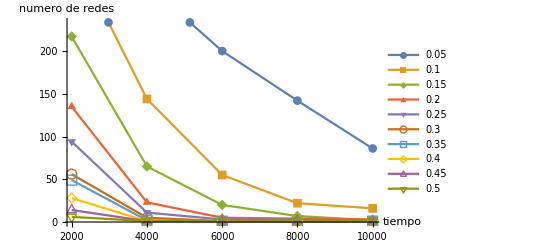

```mathematica
ListLinePlot[{datosPlot005,datosPlot010,datosPlot015,datosPlot020,datosPlot025,datosPlot030,datosPlot035,datosPlot040,datosPlot045,datosPlot050},AxesLabel->{"tiempo","numero de redes"},PlotLegends->{0.05,0.10,0.15,0.20,0.25,0.30,0.35,0.40,0.45,0.50},PlotMarkers->Automatic]
```

```mathematica
Map[Length,FindClique[redes[[11]],Infinity,All]]
```

```mathematica
allCliquesModelo=Table[Map[Length,FindClique[redes[[i]],Infinity,All]],{i,2,Length[time],1}];
```

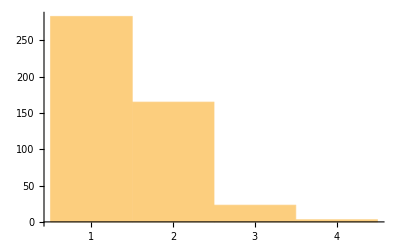
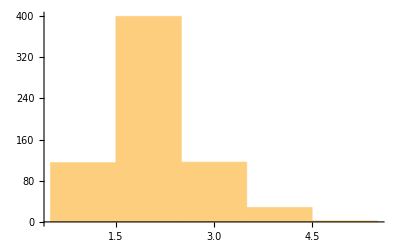
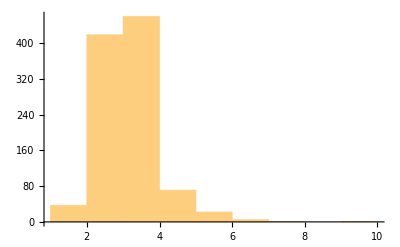
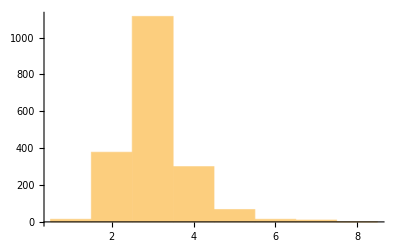
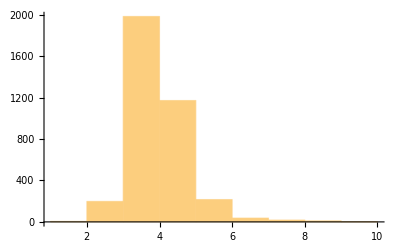
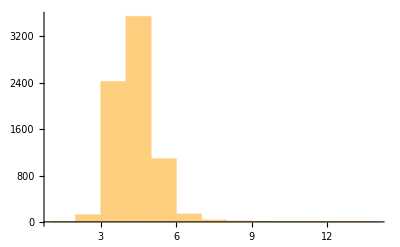
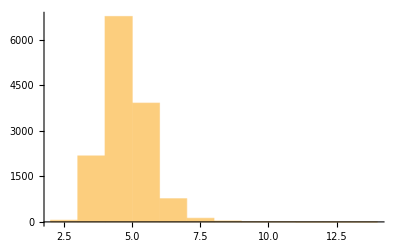
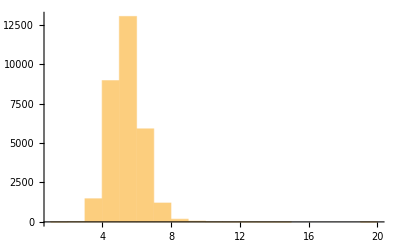

```mathematica
Map[Histogram,allCliquesModelo]
```

```mathematica
allCliquesAleatorias=Table[Map[Length,FindClique[aleatorias[[i]],Infinity,All]],{i,2,Length[time],1}];
```

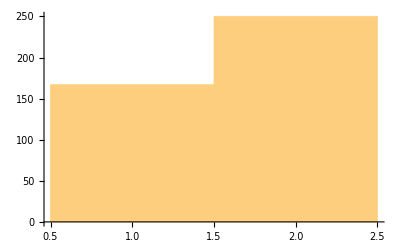
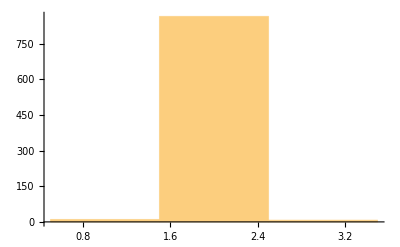
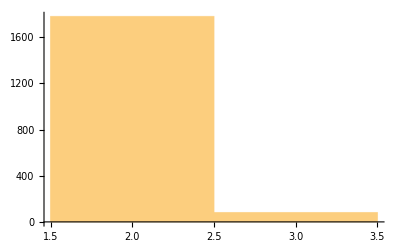
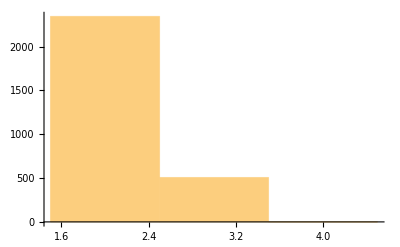
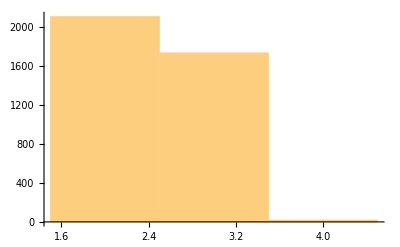
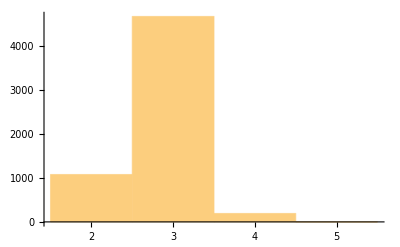
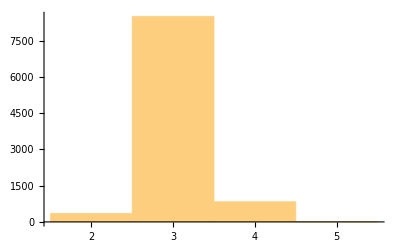
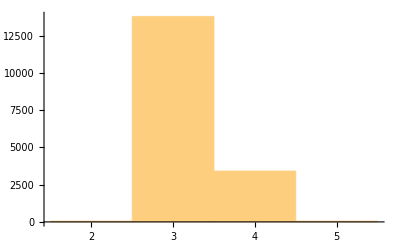

```mathematica
Map[Histogram,allCliquesAleatorias]
```